## Examen de Transformada de Funciones II

```mathematica
(*
	x'[t]-4x[t]-2y[t]==0
 y'[t]+(5/2)x[t]-2y[t]==0
  y[0]==1,x[0]==1
*)
```

```mathematica
DSolve[{x'[t]-4x[t]-2y[t]==0,y'[t]+(5/2)x[t]-2y[t]==0,y[0]==1,x[0]==1},{y[t],x[t]},t]/.Rule->Equal
```

{{x[t]==1/2 ⅇ^(3 t) (2 Cos[2 t]+3 Sin[2 t]),y[t]==1/4 ⅇ^(3 t) (4 Cos[2 t]-7 Sin[2 t])}}

```mathematica
InverseLaplaceTransform[((((s-4)s)/((s-3)^2  +4))-1)/2,s,t]//FullSimplify
```

1/4 ⅇ^(3 t) (4 Cos[2 t]-7 Sin[2 t])

```mathematica
InverseLaplaceTransform[(s- (13/2))/((s-3)^2  +4),s,t]//FullSimplify
```

1/4 ⅇ^(3 t) (4 Cos[2 t]-7 Sin[2 t])

```mathematica
InverseLaplaceTransform[(E^(-2s)  *(s-1))/(s^3  -4s^2  +5),s,t]//ExpToTrig//TrigReduce//FullSimplify
```

1/55 ⅇ^(-5-1/2 (-3+√5) t) ((5-4 √5) ⅇ^(√5+t)+(5+4 √5) ⅇ^(-√5+t+√5 t)-10 ⅇ^(7+1/2 (-5+√5) t)) HeavisideTheta[-2+t]

```mathematica
(E^(-2s)  *(s-1))/(s^3  -4s^2  +5)
```

```mathematica
(ⅇ^(-2 s) (-1+s))/(5s-4 s^2+s^3)
```

```mathematica
Apart[(-1+s)/(5s-4 s^2+s^3)]
```

-1/(5 s)+(1+s)/(5 (5-4 s+s^2))

```mathematica
InverseLaplaceTransform[-1/(5 s)*ⅇ^(-2 s),s,t]
(1/5)* InverseLaplaceTransform[(s+1)/((s-2)^2  +1)*ⅇ^(-2 s),s,t]//FullSimplify
(%%+%)//FullSimplify(*Resultado*)
```

-1/5 HeavisideTheta[-2+t]

1/5 ⅇ^(-4+2 t) HeavisideTheta[-2+t] (Cos[2-t]-3 Sin[2-t])

1/5 HeavisideTheta[-2+t] (-1+ⅇ^(-4+2 t) (Cos[2-t]-3 Sin[2-t]))

Piecewise[{{-1, -2≤t<0}, {1, 0≤t<2}, {0, True}}]

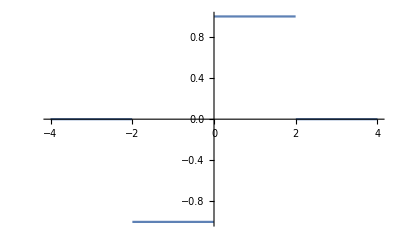

-(2 (-1+Cos[n π]))/(n π)

```mathematica
Piecewise[{{-1,-2≤t<0},{1,0≤t<2}}]
Plot[%,{t,-4,4}]
Integrate[(%%)*Sin[n*Pi/2  *t],{t,0,2}](*Coeficiente de bn*)
```

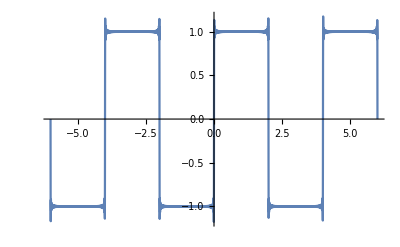

```mathematica
Simplify[-(2 (-1+Cos[n π]))/(n π),n∈Integers];
Sum[(%)*Sin[n*Pi/2  *t],{n,300}];
Plot[%,{t,-6,6}]
```

```mathematica
2HeavisideTheta[t]-2*HeavisideTheta[t-1]
```

-2 HeavisideTheta[-1+t]+2 HeavisideTheta[t]

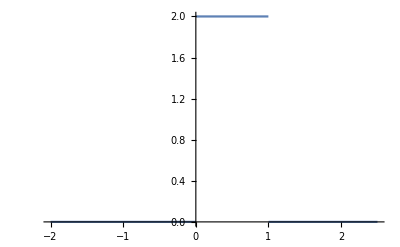

```mathematica
Plot[-2 HeavisideTheta[-1+t]+2 HeavisideTheta[t],{t,-2,2.5}]
```